8

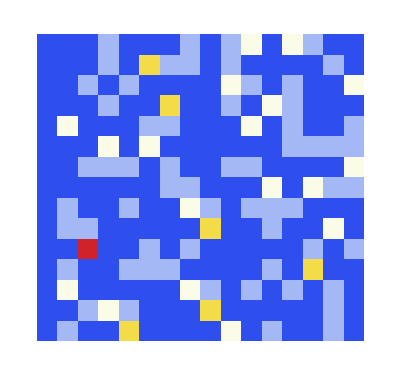

```mathematica
dm=Max[mm=Drop[DDT[S],1]]
ArrayPlot[mm,ColorFunction->"TemperatureMap"]
```

```mathematica
Position[mm,dm]
```

{{11,3}}

```mathematica
cycle=FindCycle[edges,Infinity,All];
LayeredGraph[Union[Join@@cycle]]
HighlightGraph[edges,cycle]
```

LayeredGraph::graph: A graph object is expected at position 1 in LayeredGraph[Join[All,edges,∞]].

LayeredGraph[Join[All,edges,∞]]

HighlightGraph[edges,FindCycle[edges,∞,All]]